```mathematica
ClearAll
(* Constants needed etc. *)
a=1;
β=1;
m=1;
(* Numerical stuff - come back to it *)
(*

NUMB[ρ_]:=a^2/(4π)NIntegrate[(a^2-ρ a Cos[ϕ])/((ρ^2+(β a)^2+a^2-2 a ρ Cos[ϕ])^(3/2)),{ϕ,0.1,2π}];
sol=NDSolve[{D[A[ρ],ρ]+A[ρ]/ρ==NUMB[ρ],A[0.001]=0},A,{ρ,0,10a}];
A=First[A/.sol]; 
*)

(* Define vector potential and simplify to scalar expression, assuming B(ρ) -> Subscript[B, z] *)
VECA[ρ_]:=ρ Exp[-ρ^2/(2 a^2)]; 
SCALA[ρ_]:=VECA[ρ]^2-2/ρ m VECA[ρ];
```

ClearAll

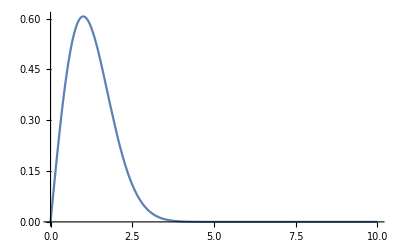

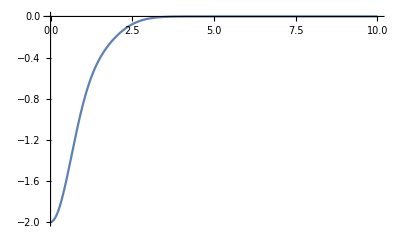

```mathematica
Plot[{VECA[ρ]}, {ρ,0,10},PlotRange->All]
Plot[{SCALA[ρ]}, {ρ,0,10},PlotRange->All]
```

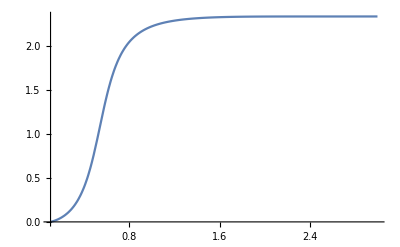

```mathematica
(* Recursive solver for Riccati type differential equation for phase shift. Plateaus in the produced figure denote bound states and should correspond to multiples of π. *)
PShift[ρ]=0.5;
For[i = 0, i < 100, i++,
placeholder=NDSolveValue[{PShift'[ρ]==-π/2*ρ* SCALA[ρ]*(BesselJ[0,0.1* ρ]*Cos[PShift[ρ]]-BesselY[0,0.1* ρ]*Sin[PShift[ρ]])^2,PShift[0.1]==0},PShift, {ρ,0.1,10}];
PShift[ρ]=placeholder[ρ]
]
Plot[PShift[ρ], {ρ,0.1,3}]
```